# Release Energy: 1. LHY gas from trap 2. from droplet to LHY gas

v1 - 2021.02.02

v2 - 2021.03.02

Abstract

In this note, I try to distinguish two different type of expansion of LHY gas: 
1. LHY gas directly releasing from trap
2. after phase transition from droplet then expanding. 
The first one contains the information of trap frequency but the latter one not. Main different comes from the origin of kinetic energy of the sample. LHY gas in trap possess kinetic energy mainly induced by the confinement of trap, however, the latter one’s kinetic energy come from the confinement of itself (or surface tension). From this point of view, we can understand that the abnormal raising expansion velocity when δg get even negative in the droplet-to-gas case.

## Two type of expansion

### From droplet to LHY gas

With the rough calculation from Gaussian variational method, we can get the Energy of droplet sample as a function of its size. From bottom to top, each curve represents a sample with a atomic number. When number is large, droplet solution is the energy with very negative value. With number loss, if considering an adiabatic process (i.e. the number loss time scale is much smaller than the droplet characteristic time scale), we can have the droplet sample follows the black-arrow. When the energy solution gets to above zero, we have a meta-stable droplet. Finally, when the local minimum disappear, we have the liquid-to-gas phase transition.

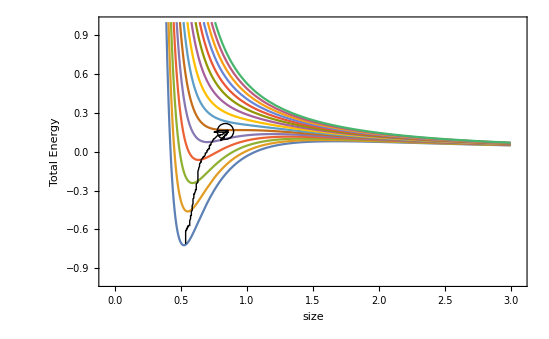

After the droplet sample turning to a LHY-gas sample, its state will just stay at the unstable-equilibrium point (i.e. the black circle). Then, it will just expands and releases energy, including kinetic, MF and LHY energy. After large enough time expansion, when its size getting large enough and density getting low enough, we can say that all energy turns to the expanding-energy, which just equals to the total energy of the droplet sample when phase transition happened.

### Calculation and compare with experiment

The droplet energy calculated by Gaussian Ansatz is

E_tot[w]=N ℏ ω (3/4 1/w^2+1/(√(2π))(a_S N)/a_C 1/w^3+512/(75 π^(7/4))√(2/5)(A/a_C)^(5/2)N^(3/2)1/w^(9/2))

and other parameters are defined as

The effective number is

N=N_-=(N_Rb √g_Na+N_Na √g_Rb)/(√(g_Na+g_Rb))=(√(g_Na+g_Rb))/(√g_Rb)N_Na=1.747 N_Na, N/N_tot=0.718

effective mass is

m=(N m_Na m_Rb)/(N_Na m_Rb+N_Rb m_Na)=(1.747 m_Na m_Rb)/(m_Rb+1.433 m_Na)=1.267 m_Na

Mean field energy is

(4π ℏ^2 a_S)/m=2 λ_-=(2δg √(g_Rb g_Na))/(g_Na+g_Rb), where  δg=g_(Rb,Na)+√(g_Rb g_Na), 
i.e. a_S=(m √(g_Na g_Rb))/(4π ℏ^2)OverTilde[δg], i.e. a_S/a_C=2.5508*10^-3*OverTilde[δg]

LHY energy is

A=m/(4π ℏ^2) (m_Na^(3/5)g_Na N_Na+m_Rb^(3/5)g_Rb N_Rb)/(m^(3/5)N)
i.e. A=(1.267 m_Na g_Na)/(4π ℏ^2) (1+(3.78)^(3/5)*0.487*1.433)/((1.267)^(3/5)1.747)=(1.604 m_Na g_Na)/(4π ℏ^2)=1.604 a_Na

Here we take characteristic length a_C, which also define a energy scale

ω=ℏ/(m a_C^2)

Note that this characteristic length can be arbitrary. We take

a_C=1μm, ω=2π*344.498Hz (i.e. 16.533nK)

Then, we get

A/a_C=4.626*10^-3

We take the first and second derivative of energy to get the max and min point, then get the phase transition point.

```mathematica
D[(3/4 1/w^2+1/(√(2π))(as*Nn)/w^3+512/(75 π^(7/4))√(2/5)A^2.5*Nn^1.5 1/w^(9/2)), w]
D[(3/4 1/w^2+1/(√(2π))(as*Nn)/w^3+512/(75 π^(7/4))√(2/5)A^2.5*Nn^1.5 1/w^(9/2)), w,w]
```

-(768 √(2/5) A^2.5 Nn^1.5)/(25 π^(7/4) w^(11/2))-(3 as Nn)/(√(2 π) w^4)-3/(2 w^3)

(4224 √(2/5) A^2.5 Nn^1.5)/(25 π^(7/4) w^(13/2))+(6 as Nn √(2/π))/w^5+9/(2 w^4)

```mathematica
f4[Nn_,δg_]:=NSolve[-(768 √(2/5) (4.626*10^-3)^2.5 Nn^1.5)/(25 π^(7/4) w^(11/2))-(3 (2.5508*10^-3*δg) Nn)/(√(2 π) w^4)-3/(2 w^3)==0,w,Reals];
f5[Nn_,δg_]:=(4224 √(2/5) (4.626*10^-3)^2.5 Nn^1.5)/(25 π^(7/4) w^(13/2))+(6 (2.5508*10^-3*δg) Nn √(2/π))/w^5+9/(2 w^4);
```

Then, we get droplet energy, size and the maximum point:

```mathematica
EdropletPoints[n0_,δg0_]:=Module[{n=n0,δg=δg0},sol=f4[10^n,δg];sol=Select[sol,(f5[10^n,δg]/.#)≥0&];Table[{n,δg,16.533*0.718(3/4 1/w^2+1/(√(2π))((2.5508*10^-3*δg)*10^n)/w^3+512/(75 π^(7/4))√(2/5)(4.626*10^-3)^2.5*(10^n)^1.5 1/w^(9/2))/.sol[[i]],16.533*0.718(3/4 1/w^2)/.sol[[i]],16.533*0.718(1/(√(2π))((2.5508*10^-3*δg)*10^n)/w^3)/.sol[[i]],16.533*0.718(512/(75 π^(7/4))√(2/5)(4.626*10^-3)^2.5*(10^n)^1.5 1/w^(9/2))/.sol[[i]]},{i,1,Length@sol,1}]];
DropletSize[n0_,δg0_]:=Module[{n=n0,δg=δg0},sol=f4[10^n,δg];sol=Select[sol,(f5[10^n,δg]/.#)≥0&];Table[{n,δg,w/.sol[[i]]},{i,1,Length@sol,1}]];
EmaxdropletPoints[n0_,δg0_]:=Module[{n=n0,δg=δg0},sol=f4[10^n,δg];sol=Select[sol,(f5[10^n,δg]/.#)<0&];Table[{n,δg,16.533*0.718(3/4 1/w^2+1/(√(2π))((2.5508*10^-3*δg)*10^n)/w^3+512/(75 π^(7/4))√(2/5)(4.626*10^-3)^2.5*(10^n)^1.5 1/w^(9/2))/.sol[[i]]},{i,1,Length@sol,1}]];
```

```mathematica
dataD31=Flatten[ParallelTable[EdropletPoints[n,δg],{δg,-0.25,-0.02,0.02},{n,2,6,0.02}],2];
```

```mathematica
dataD41=Flatten[ParallelTable[EmaxdropletPoints[n,δg],{δg,-0.25,-0.05,0.02},{n,2,6,0.02}],2];
```

```mathematica
tempA=Sort[#,#1[[3]]>#2[[3]]&]&/@Gather[dataD41,#1[[2]]==#2[[2]]&];
tempB=Sort[#,#1[[3]]>#2[[3]]&]&/@Gather[dataD31,#1[[2]]==#2[[2]]&];
```

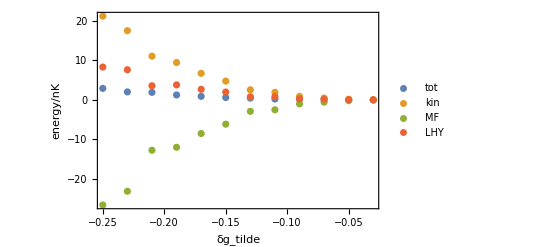

```mathematica
temp1=#[[1]]&/@tempA;
temp2=#[[1]]&/@tempB;
ListPlot[{temp2[[All,{2,3}]],temp2[[All,{2,4}]],temp2[[All,{2,5}]],temp2[[All,{2,6}]]},PlotLegends->{"tot","kin","MF","LHY"},PlotRange->All,Frame->True,FrameLabel->{"δg_tilde","energy/nK"}]
```

```mathematica
temp2[[All,{2,3}]]
```

{{-0.25,2.90794},{-0.23,2.01714},{-0.21,1.89391},{-0.19,1.24729},{-0.17,0.901294},{-0.15,0.589653},{-0.13,0.452032},{-0.11,0.223117},{-0.09,0.149006},{-0.07,0.0653223},{-0.05,0.0251234},{-0.03,0.00513879}}

```mathematica
Export["C:\\Users\\Administrator.WIN-KQNL4VO8QRH\\Desktop\\origin temp\\temp.txt",temp2[[All,{2,3}]],"Table"]
```

C:\Users\Administrator.WIN-KQNL4VO8QRH\Desktop\origin temp\temp.txt

```mathematica
ListPlot3D[{dataD31,dataD41},PlotRange->All]
```

-Graphics3D-

```mathematica
dataD51=Flatten[ParallelTable[DropletSize[n,δg],{δg,-0.3,-0.05,0.02},{n,2,6,0.02}],2];
ListPlot3D@dataD51
```

-Graphics3D-

```mathematica
temp1
```

{{2.4,-0.3,2.72361},{2.48,-0.28,2.13847},{2.56,-0.26,1.71752},{2.64,-0.24,1.41699},{2.74,-0.22,1.05029},{2.84,-0.2,0.808281},{2.96,-0.18,0.567032},{3.08,-0.16,0.42053},{3.22,-0.14,0.292194},{3.4,-0.12,0.168268},{3.6,-0.1,0.0960495},{3.84,-0.08,0.049934},{4.14,-0.06,0.0229905}}

### LHY gas released from trap

For LHY gas sample releasing from trap, as we discussed before, the release energy have been well defined as the summation of kinetic energy in trap and all interaction energy. In this case, the information of trap remains, however for the expansion of droplet-to-gas sample, the information of trap already disappeared.

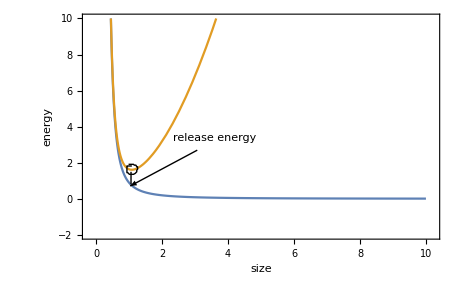

We lot the release energy as a function of both δg and atomic number

-Graphics3D-

The blue dots represents the release energy and number is ranging from 10^3 to 10^5, (note that here the δg is not what we defined before, with a scale difference)

## Plot

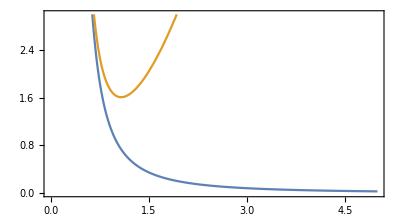

```mathematica
p1=Plot[Evaluate[(3/4(1/w^2+{0,1}w^2)+1/(√(2π))χ/w^3+512/(75 π^(7/4))√(2/5)ξ 1/w^(9/2))/.{χ->-0.1,ξ->0.3}],{w,0.1,5},PlotRange->{0,3},Frame->True,AspectRatio->1/0.618/3]
```

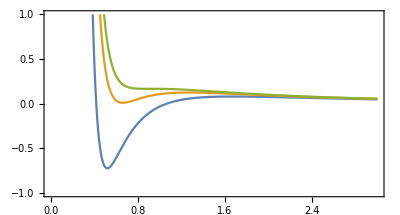

```mathematica
p2=Plot[Evaluate[Table[(3/4(1/w^2+{0}w^2)+1/(√(2π))χ/w^3+512/(75 π^(7/4))√(2/5)ξ 1/w^(9/2))/.{χ->chi0,ξ->0.3},{chi0,{-2.4,-2.05,-1.9}}]],{w,0.1,3},PlotRange->{-1,1},Frame->True,AspectRatio->1/0.618/3]
```

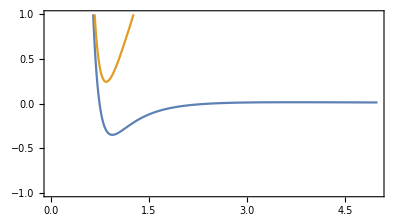

```mathematica
chi=-0.00045*11500;xi=0.0045^2.5*11500^1.5;
p1=Plot[Evaluate[(3/4(1/w^2+{0,1}w^2)+1/(√(2π))χ/w^3+512/(75 π^(7/4))√(2/5)ξ 1/w^(9/2))/.{χ->chi,ξ->xi}],{w,0.1,5},PlotRange->{-1,1},Frame->True,AspectRatio->1/0.618/3]
```

```mathematica
d1=Table[Flatten@{w,Evaluate[(3/4(1/w^2+{0,1}w^2)+1/(√(2π))χ/w^3+512/(75 π^(7/4))√(2/5)ξ 1/w^(9/2))/.{χ->chi,ξ->xi}]},{w,0.1,10,0.05}];
```

```mathematica
Export["D:\\Dropbox\\@Droplet\\@Calculations\\LHY gas expansion and released energy\\d1.txt",d1,"Table"]
```

D:\Dropbox\@Droplet\@Calculations\LHY gas expansion and released energy\d1.txt